# Yule Model

## Simulations

```mathematica
Clear[sim]
sim[λ_,intS_]:=sim[λ,intS]=Block[{out,Δt},out={{0,1}};
Δt=RandomVariate[ExponentialDistribution[λ out[[-1,2]]]];
While[out[[-1,1]]+Δt<1,
AppendTo[out,out[[-1]]+{Δt,1}];
Δt=RandomVariate[ExponentialDistribution[λ out[[-1,2]]]];
];
AppendTo[out,{1,out[[-1,2]]}];
out
]
```

## Fitting the Cases

```mathematica
f[n_,τ_]:=-λ P[n,τ]+λ Sum[P[j,τ]P[n-j,τ],{j,0,n}]
```

```mathematica
{D[P[0,τ],τ]==f[0,τ],P[0,0]==0}
```

{P^(0,1)[0,τ]==-λ P[0,τ]+λ P[0,τ]^2,P[0,0]==0}

```mathematica
Clear[odes,vars]
```

```mathematica
odes[kMax_]:=odes[kMax]=Join[Table[D[P[k,τ],τ]==f[k,τ]/.P[0,τ]->0,{k,1,kMax}],Table[If[k==1,P[k,0]==1,P[k,0]==0],{k,1,kMax}]];
vars[kMax_]:=vars[kMax]=Table[P[k,τ],{k,1,kMax}];
```

```mathematica
DSolve[odes[4],vars[4],{τ,0,1}][[1]]
```

{P[1,τ]→ⅇ^(-λ τ),P[2,τ]→ⅇ^(-2 λ τ) (-1+ⅇ^(λ τ)),P[3,τ]→ⅇ^(-3 λ τ) (-1+ⅇ^(λ τ))^2,P[4,τ]→ⅇ^(-4 λ τ) (-1+ⅇ^(λ τ))^3}

```mathematica
Psol[k_]:=Exp[-k λ 1](Exp[ λ 1]-1)^(k-1)
```

```mathematica
Plog[k_]:=-k λ +(k-1)Log[Exp[λ]-1]
```

```mathematica
Solve[{D[Plog[k],λ]==0,λ>0},λ][[1]]
```

{λ→ConditionalExpression[Log[k], k>1]}

```mathematica
λPlot[k_]:=Plot[{Plog[k],Evaluate[N[Plog[k]/.λ->Log[k]]],Evaluate[N[Plog[k]/.λ->Log[k]]-2]},{λ,4,10},PlotStyle->{Black,Red,{Red,Dashed}}]
```

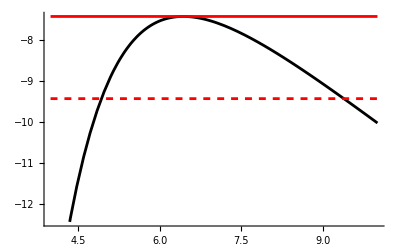

```mathematica
λPlot[624]
```

```mathematica
FitCases[k_]:=Block[{λEst,λmin,λmax,temp},
λEst=Log[k]//N;
temp=Evaluate[N[Plog[k]/.λ->λEst]-2];
λmin=λ/.FindRoot[Plog[k]==temp,{λ,Max[λEst-0.25,0]}];
λmax=λ/.FindRoot[Plog[k]==temp,{λ,λEst+0.25}];
{λmin,λEst,λmax}
]
```

```mathematica
λtemp=6;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

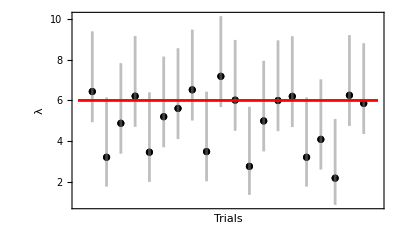

```mathematica
fitList=Table[FitCases[sim[λtemp,intS][[-1,2]]],{intS,1,20}];
Show[ListPlot[Table[{{j,fitList[[j,2]]}},{j,1,20}],PlotStyle->Black],ListLinePlot[Table[{{j,fitList[[j,1]]},{j,fitList[[j,3]]}},{j,1,20}],PlotStyle->Directive[Gray,Opacity[0.5]]],Plot[λtemp,{j,0,21},PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"Trials","λ"},FrameTicks->{{True,False},{False,False}},LabelStyle->Directive[Black, Medium]]
```

## Phylogenetic Fit

### Phylogenetic Likelihood

```mathematica
ϕArg[λ_,τ_]:=-λ τ
```

```mathematica
xVec[λtrue_,intS_]:=1-sim[λtrue,intS][[2;;-2,1]]
```

```mathematica
Clear[ℓP]
ℓP[λin_,λtrue_,intS_]:=Block[{out},
out=Join[{ϕArg[λin,1]},Map[Log[λin]+ ϕArg[λin,#]&,xVec[λtrue,intS]]];
out//Total]
```

```mathematica
Clear[ℓPTab]
ℓPTab[λtrue_,intS_]:=ℓPTab[λtrue,intS]=Table[{λin,ℓP[λin,λtrue,intS]},{λin,λtrue/5,2λtrue,0.05}]
```

```mathematica
MPE[λtrue_,intS_]:=Sort[ℓPTab[λtrue,intS],#1[[2]]>#2[[2]]&][[1]]
```

```mathematica
Clear[CI]
CI[λtrue_,intS_]:=CI[λtrue,intS]=Select[ℓPTab[λtrue,intS],#[[2]]>MPE[λtrue,intS][[2]]-2&]
CILen[λtrue_,intS_]:=Max[CI[λtrue,intS][[;;,1]]]-Min[CI[λtrue,intS][[;;,1]]]
```

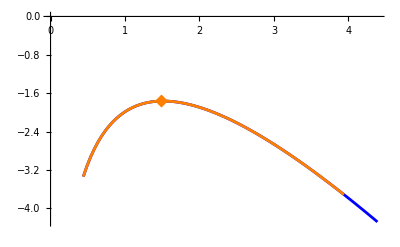

```mathematica
ListPlot[{ℓPTab[2.2,3],CI[2.2,3],{MPE[2.2,3]}},Joined->{True,True,False},PlotStyle->{Blue,Orange,Orange},PlotMarkers->{None,None,{Automatic,13}}]
```

```mathematica
Solve[D[-λ+(n-1)Log[λ]-λ X,λ]==0,λ]
```

{{λ→(-1+n)/(1+X)}}

```mathematica
λtest[λtrue_,intS_]:=(*Length[xVec[λtrue,intS]]/(1+Total[xVec[λtrue,intS]])*)1/(1/Length[xVec[λtrue,intS]]+Mean[xVec[λtrue,intS]])
```

```mathematica
MPE[6,1]
```

{6.3,522.897}

```mathematica
λtest[6,1]
```

6.29227

```mathematica
plot1[λTrue_,nSim_]:=Show[
(*True*)
ListLinePlot[{{λTrue,0},{λTrue,nSim+1}},PlotStyle->Red],
(*Case*)
ListPlot[Table[{FitCases[sim[λTrue,intS][[-1,2]]][[2]],intS+0.25},{intS,1,nSim}],PlotStyle->Blue],
ListLinePlot[Table[{{FitCases[sim[λTrue,intS][[-1,2]]][[1]],intS+0.25},{FitCases[sim[λTrue,intS][[-1,2]]][[3]],intS+0.25}},{intS,1,nSim}],PlotStyle->Directive[Blue,Opacity[0.3]]],
(*Phylogeny*)
ListPlot[Table[{MPE[λTrue,intS][[1]],intS},{intS,1,nSim}],PlotStyle->Orange],
ListLinePlot[Table[Map[{#,intS}&,CI[λTrue,intS][[;;,1]]],{intS,1,nSim}],PlotStyle->Directive[Orange,Opacity[0.3]]],Frame->True,FrameLabel->{"λ","Trials"},FrameTicks->{{False,False},{True,False}},LabelStyle->Directive[Black, Medium]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

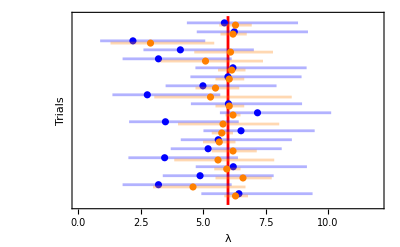

```mathematica
plot1[6,20]
```

```mathematica
Table[Abs[MPE[6,intS][[1]]-6],{intS,1,20}]//Mean
```

0.5

```mathematica
Table[Abs[FitCases[sim[6,intS][[-1,2]]][[2]]-6],{intS,1,20}]//Mean
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.29024

```mathematica
Table[FitCases[sim[6,intS][[-1,2]]][[3]]-FitCases[sim[6,intS][[-1,2]]][[1]],{intS,1,20}]//Mean
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

4.41117

```mathematica
Table[CILen[6,intS],{intS,1,20}]//Mean
```

2.2475